

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
D[x^3-x,x]
```

-1+3 x^2

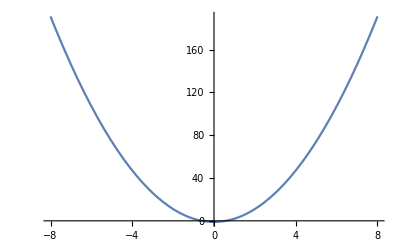

```mathematica
Plot[-1+3 x^2,{x,-8,8}]
```

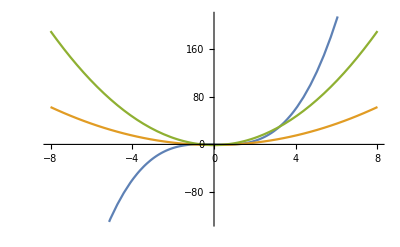

```mathematica
Plot[{x^3-x,x^2-1,-1+3 x^2},{x,-8,8}]
```

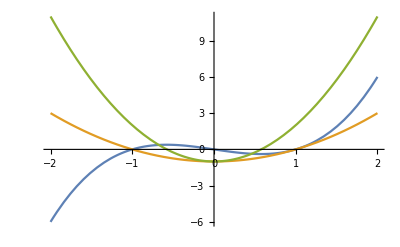

```mathematica
Plot[{x^3-x,x^2-1,-1+3 x^2},{x,-2,2}]
```

```mathematica
Table[(x^3-x)/x^i,{i,0,4}]
```

{-x+x^3,(-x+x^3)/x,(-x+x^3)/x^2,(-x+x^3)/x^3,(-x+x^3)/x^4}

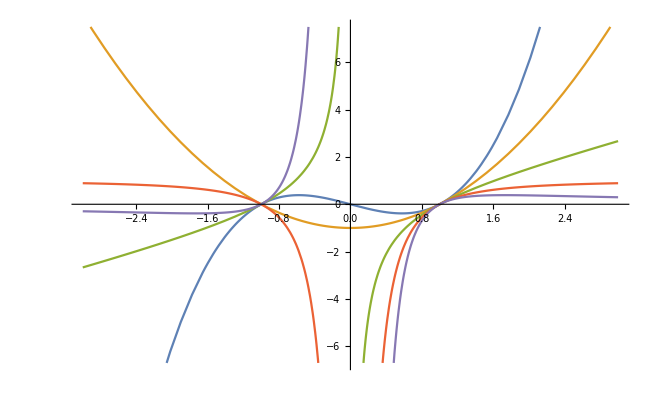

```mathematica
Plot[{-x+x^3,(-x+x^3)/x,(-x+x^3)/x^2,(-x+x^3)/x^3,(-x+x^3)/x^4},{x,-3,3}]
```

```mathematica
Map[Function[x,#]&,{-x+x^3,(-x+x^3)/x,(-x+x^3)/x^2,(-x+x^3)/x^3,(-x+x^3)/x^4}]
```

{Function[x,-x+x^3],Function[x,(-x+x^3)/x],Function[x,(-x+x^3)/x^2],Function[x,(-x+x^3)/x^3],Function[x,(-x+x^3)/x^4]}

```mathematica
Map[(#''[x])/((√(1+(#'[x])^2))^3)&,{Function[x,-x+x^3],Function[x,(-x+x^3)/x],Function[x,(-x+x^3)/x^2],Function[x,(-x+x^3)/x^3],Function[x,(-x+x^3)/x^4]}]
```

{(6 x)/((1+(-1+3 x^2)^2)^(3/2)),(6-(2 (-1+3 x^2))/x^2-(2 (x-x^3))/x^3)/((1+((-1+3 x^2)/x-(-x+x^3)/x^2)^2)^(3/2)),(6/x-(4 (-1+3 x^2))/x^3+(6 (-x+x^3))/x^4)/((1+((-1+3 x^2)/x^2-(2 (-x+x^3))/x^3)^2)^(3/2)),(6/x^2-(6 (-1+3 x^2))/x^4+(12 (-x+x^3))/x^5)/((1+((-1+3 x^2)/x^3-(3 (-x+x^3))/x^4)^2)^(3/2)),(6/x^3-(8 (-1+3 x^2))/x^5+(20 (-x+x^3))/x^6)/((1+((-1+3 x^2)/x^4-(4 (-x+x^3))/x^5)^2)^(3/2))}

```mathematica
FullSimplify[{(6 x)/((1+(-1+3 x^2)^2)^(3/2)),(6-(2 (-1+3 x^2))/x^2-(2 (x-x^3))/x^3)/((1+((-1+3 x^2)/x-(-x+x^3)/x^2)^2)^(3/2)),(6/x-(4 (-1+3 x^2))/x^3+(6 (-x+x^3))/x^4)/((1+((-1+3 x^2)/x^2-(2 (-x+x^3))/x^3)^2)^(3/2)),(6/x^2-(6 (-1+3 x^2))/x^4+(12 (-x+x^3))/x^5)/((1+((-1+3 x^2)/x^3-(3 (-x+x^3))/x^4)^2)^(3/2)),(6/x^3-(8 (-1+3 x^2))/x^5+(20 (-x+x^3))/x^6)/((1+((-1+3 x^2)/x^4-(4 (-x+x^3))/x^5)^2)^(3/2))},x∈Reals]
```

{(6 x)/((1+(1-3 x^2)^2)^(3/2)),2/((1+4 x^2)^(3/2)),-(2 x^3)/((1+2 (x^2+x^4))^(3/2)),-(6 Abs[x]^5)/((4+x^6)^(3/2)),(2 x^7 (-6+x^2))/((9-6 x^2+x^4+x^8)^(3/2))}

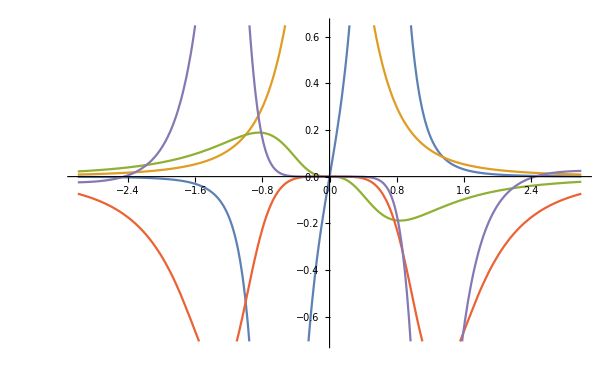

```mathematica
Plot[
{(6 x)/((1+(1-3 x^2)^2)^(3/2)),2/((1+4 x^2)^(3/2)),-(2 x^3)/((1+2 (x^2+x^4))^(3/2)),-(6 Abs[x]^5)/((4+x^6)^(3/2)),(2 x^7 (-6+x^2))/((9-6 x^2+x^4+x^8)^(3/2))}
,{x,-3,3}]
```

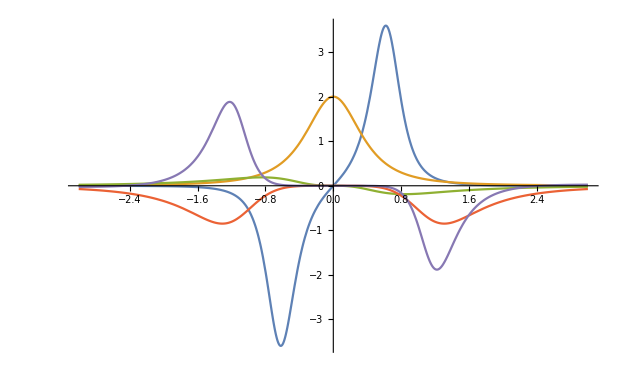

```mathematica
Plot[
{(6 x)/((1+(1-3 x^2)^2)^(3/2)),2/((1+4 x^2)^(3/2)),-(2 x^3)/((1+2 (x^2+x^4))^(3/2)),-(6 Abs[x]^5)/((4+x^6)^(3/2)),(2 x^7 (-6+x^2))/((9-6 x^2+x^4+x^8)^(3/2))}
,{x,-3,3},PlotRange->Full]
```

```mathematica
Solve[α x^3-x==x^3,α,Reals]
```

{{α→(x+x^3)/x^3}}

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
f''[x]/((√(1+f'[x]^2))^3)== ⅇ^(-x^2/2)
```

f''[x]/((1+f'[x]^2)^(3/2))==ⅇ^(-x^2/2)

```mathematica
DSolve[f''[x]/((1+f'[x]^2)^(3/2))==ⅇ^(-x^2/2),{f[x],f[x]},{x}]
```

{{f[x]→C[2]+-(√(-2 C[1]^2-2 √(2 π) C[1] Erf[K[1]/(√2)]-π Erf[K[1]/(√2)]^2))/(√(-2+2 C[1]^2+2 √(2 π) C[1] Erf[K[1]/(√2)]+π Erf[K[1]/(√2)]^2))K[1]1x},{f[x]→C[2]+(√(-2 C[1]^2-2 √(2 π) C[1] Erf[K[2]/(√2)]-π Erf[K[2]/(√2)]^2))/(√(-2+2 C[1]^2+2 √(2 π) C[1] Erf[K[2]/(√2)]+π Erf[K[2]/(√2)]^2))K[2]1x}}

```mathematica
-(√(-2 C[1]^2-2 √(2 π) C[1] Erf[K[1]/(√2)]-π Erf[K[1]/(√2)]^2))/(√(-2+2 C[1]^2+2 √(2 π) C[1] Erf[K[1]/(√2)]+π Erf[K[1]/(√2)]^2))K[1]1x/.K[1]->t
```

-(√(-2 C[1]^2-2 √(2 π) C[1] Erf[t/(√2)]-π Erf[t/(√2)]^2))/(√(-2+2 C[1]^2+2 √(2 π) C[1] Erf[t/(√2)]+π Erf[t/(√2)]^2))t1x

```mathematica
Activate[-(√(-2 C[1]^2-2 √(2 π) C[1] Erf[t/(√2)]-π Erf[t/(√2)]^2))/(√(-2+2 C[1]^2+2 √(2 π) C[1] Erf[t/(√2)]+π Erf[t/(√2)]^2))t1x]
```

$Aborted

```mathematica
-(√(-2 C[1]^2-2 √(2 π) C[1] Erf[t/(√2)]-π Erf[t/(√2)]^2))/(√(-2+2 C[1]^2+2 √(2 π) C[1] Erf[t/(√2)]+π Erf[t/(√2)]^2))t1x/.C[1] ->1
```

-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2))/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2))t1x

```mathematica
Activate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2))/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2))t1x]
```

∫_1^x -(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2))/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2))ⅆt

```mathematica
Table[NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2))/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2))ⅆt,{t,1,a}],{a,2,10,.1}]
```

NIntegrate::inumr: The integrand -(ⅆt √(-2-2 √(2 π) Erf[t/(√2)]-π Erf[Power[«2»] t]^2))/(√(2 √(2 π) Erf[t/(√2)]+π Erf[Power[«2»] t]^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1,2.}}.

NIntegrate::inumr: The integrand -(ⅆt √(-2-2 √(2 π) Erf[t/(√2)]-π Erf[Power[«2»] t]^2))/(√(2 √(2 π) Erf[t/(√2)]+π Erf[Power[«2»] t]^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1,2.1}}.

NIntegrate::inumr: The integrand -(ⅆt √(-2-2 √(2 π) Erf[t/(√2)]-π Erf[Power[«2»] t]^2))/(√(2 √(2 π) Erf[t/(√2)]+π Erf[Power[«2»] t]^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1,2.2}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::nlim: t = a is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2) ⅆt)/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}]}

```mathematica
Table[NIntegrate[-(√(-2-2 √(2 π) Erf[t/(√2)]-π Erf[t/(√2)]^2))/(√(2 √(2 π) Erf[t/(√2)]+π Erf[t/(√2)]^2)),{t,1,a}],{a,2,10,.1}]
```

{0.-1.14447 ⅈ,0.-1.2567 ⅈ,0.-1.36879 ⅈ,0.-1.48077 ⅈ,0.-1.59265 ⅈ,0.-1.70446 ⅈ,0.-1.81622 ⅈ,0.-1.92793 ⅈ,0.-2.03962 ⅈ,0.-2.15127 ⅈ,0.-2.26291 ⅈ,0.-2.37454 ⅈ,0.-2.48616 ⅈ,0.-2.59776 ⅈ,0.-2.70937 ⅈ,0.-2.82097 ⅈ,0.-2.93256 ⅈ,0.-3.04416 ⅈ,0.-3.15575 ⅈ,0.-3.26735 ⅈ,0.-3.37894 ⅈ,0.-3.49053 ⅈ,0.-3.60212 ⅈ,0.-3.71371 ⅈ,0.-3.8253 ⅈ,0.-3.93689 ⅈ,0.-4.04848 ⅈ,0.-4.16008 ⅈ,0.-4.27167 ⅈ,0.-4.38326 ⅈ,0.-4.49485 ⅈ,0.-4.60644 ⅈ,0.-4.71803 ⅈ,0.-4.82962 ⅈ,0.-4.94121 ⅈ,0.-5.0528 ⅈ,0.-5.16439 ⅈ,0.-5.27598 ⅈ,0.-5.38758 ⅈ,0.-5.49917 ⅈ,0.-5.61076 ⅈ,0.-5.72235 ⅈ,0.-5.83394 ⅈ,0.-5.94553 ⅈ,0.-6.05712 ⅈ,0.-6.16871 ⅈ,0.-6.2803 ⅈ,0.-6.39189 ⅈ,0.-6.50348 ⅈ,0.-6.61508 ⅈ,0.-6.72667 ⅈ,0.-6.83826 ⅈ,0.-6.94985 ⅈ,0.-7.06144 ⅈ,0.-7.17303 ⅈ,0.-7.28462 ⅈ,0.-7.39621 ⅈ,0.-7.5078 ⅈ,0.-7.61939 ⅈ,0.-7.73098 ⅈ,0.-7.84258 ⅈ,0.-7.95417 ⅈ,0.-8.06576 ⅈ,0.-8.17735 ⅈ,0.-8.28894 ⅈ,0.-8.40053 ⅈ,0.-8.51212 ⅈ,0.-8.62371 ⅈ,0.-8.7353 ⅈ,0.-8.84689 ⅈ,0.-8.95848 ⅈ,0.-9.07008 ⅈ,0.-9.18167 ⅈ,0.-9.29326 ⅈ,0.-9.40485 ⅈ,0.-9.51644 ⅈ,0.-9.62803 ⅈ,0.-9.73962 ⅈ,0.-9.85121 ⅈ,0.-9.9628 ⅈ,0.-10.0744 ⅈ}

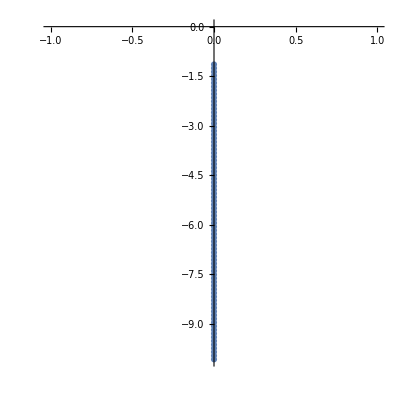

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%22,AspectRatio->1]
```

```mathematica
NIntegrate[
{(6 x)/((1+(1-3 x^2)^2)^(3/2)),2/((1+4 x^2)^(3/2)),-(2 x^3)/((1+2 (x^2+x^4))^(3/2)),-(6 Abs[x]^5)/((4+x^6)^(3/2)),(2 x^7 (-6+x^2))/((9-6 x^2+x^4+x^8)^(3/2))}
,{x,-50,50}]
```

{0.,1.9999,0.,-1.99997,0.}

```mathematica
NIntegrate[
{(6 x)/((1+(1-3 x^2)^2)^(3/2)),2/((1+4 x^2)^(3/2)),-(2 x^3)/((1+2 (x^2+x^4))^(3/2)),-(6 Abs[x]^5)/((4+x^6)^(3/2)),(2 x^7 (-6+x^2))/((9-6 x^2+x^4+x^8)^(3/2))}
,{x,0,500}]
```

{1.70711,1.,-0.292892,-1.,-1.}

```mathematica
With[{f=Function[x,x^3-x]},
FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals]
]
```

(6 x)/((1+(1-3 x^2)^2)^(3/2))

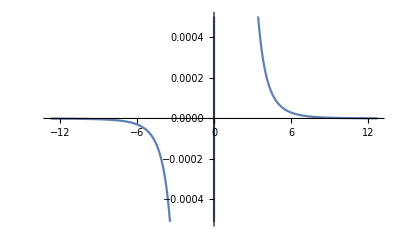

```mathematica
Plot[(6 x)/((1+(1-3 x^2)^2)^(3/2)),{x,-12.74,12.74}]
```

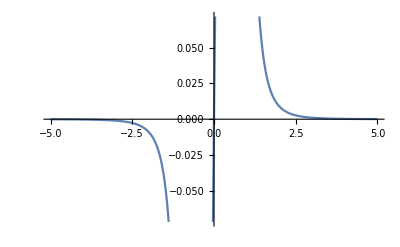

```mathematica
Plot[(6 x)/((1+(1-3 x^2)^2)^(3/2)),{x,-5,5}]
```

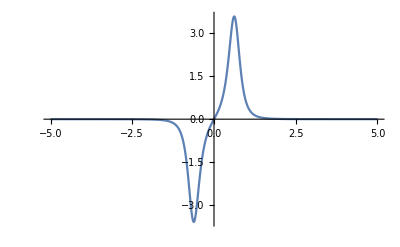

```mathematica
Plot[(6 x)/((1+(1-3 x^2)^2)^(3/2)),{x,-5,5},PlotRange->Full]
```

```mathematica
With[{f=Function[x,x^2-1]},
FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals]
]
```

2/((1+4 x^2)^(3/2))

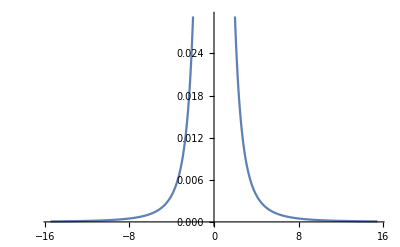

```mathematica
Plot[2/((1+4 x^2)^(3/2)),{x,-15.469999999999999,15.469999999999999}]
```

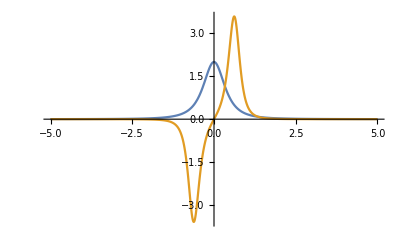

```mathematica
Plot[{2/((1+4 x^2)^(3/2)),(6 x)/((1+(1-3 x^2)^2)^(3/2))},{x,-5,5},PlotRange->Full]
```

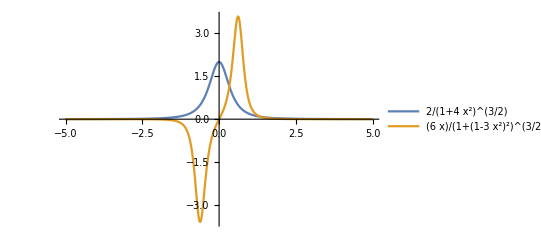

```mathematica
Plot[{2/((1+4 x^2)^(3/2)),(6 x)/((1+(1-3 x^2)^2)^(3/2))},{x,-5,5},PlotRange->Full,PlotLegends->"Expressions"]
```

```mathematica
With[{f=Function[x,x^2]},
FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals]
]
```

2/((1+4 x^2)^(3/2))

```mathematica
With[{f=Function[x,x^3]},
FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals]
]
```

(6 x)/((1+9 x^4)^(3/2))

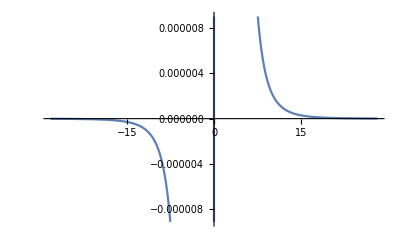

```mathematica
Plot[(6 x)/((1+9 x^4)^(3/2)),{x,-28.21,28.21}]
```

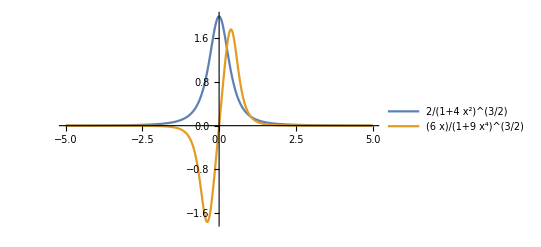

```mathematica
Plot[{2/((1+4 x^2)^(3/2)),(6 x)/((1+9 x^4)^(3/2))},{x,-5,5},PlotRange->Full,PlotLegends->"Expressions"]
```

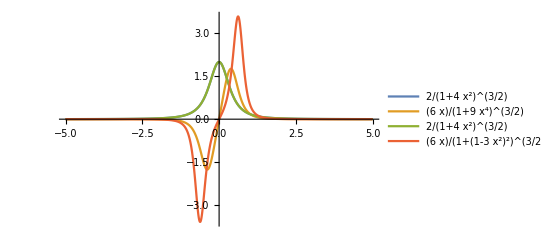

```mathematica
Plot[{2/((1+4 x^2)^(3/2)),(6 x)/((1+9 x^4)^(3/2)),2/((1+4 x^2)^(3/2)),(6 x)/((1+(1-3 x^2)^2)^(3/2))},{x,-5,5},PlotRange->Full,PlotLegends->"Expressions"]
```

```mathematica
Limit[∫_0^a (6 x)/((1+9 x^4)^(3/2))ⅆx,a->∞]
```

1

```mathematica
DivisorSigma[1,1]==2 1
```

False

```mathematica
With[{f=Function[x,x^4-x^2]},
FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals]
]
```

(-2+12 x^2)/((1+(2 x-4 x^3)^2)^(3/2))

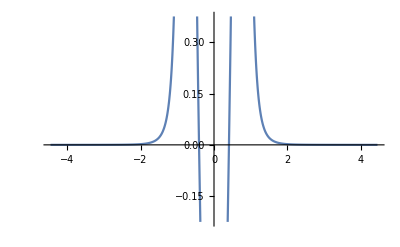

```mathematica
Plot[(-2+12 x^2)/((1+(2 x-4 x^3)^2)^(3/2)),{x,-4.458071331865384,4.458071331865384}]
```

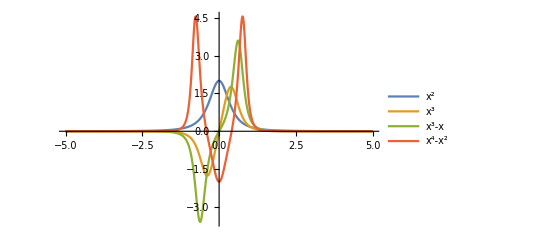

```mathematica
Plot[{2/((1+4 x^2)^(3/2)),(6 x)/((1+9 x^4)^(3/2)),(6 x)/((1+(1-3 x^2)^2)^(3/2)),(-2+12 x^2)/((1+(2 x-4 x^3)^2)^(3/2))},{x,-5,5},PlotRange->Full,PlotLegends->{x^2,x^3,x^3-x,x^4-x^2}]
```

```mathematica
With[{f=Function[x,x^4]},
FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals]
]
```

(12 x^2)/((1+16 x^6)^(3/2))

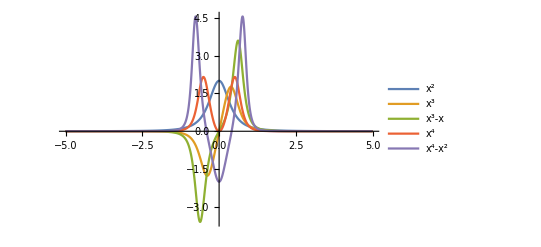

```mathematica
Plot[{2/((1+4 x^2)^(3/2)),(6 x)/((1+9 x^4)^(3/2)),(6 x)/((1+(1-3 x^2)^2)^(3/2)),(12 x^2)/((1+16 x^6)^(3/2)),(-2+12 x^2)/((1+(2 x-4 x^3)^2)^(3/2))},{x,-5,5},PlotRange->Full,PlotLegends->{x^2,x^3,x^3-x,x^4,x^4-x^2}]
```

```mathematica
Manipulate[
With[{f=Function[x,x^3+α x]},
FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals]
],{α,-2,2}]
```

```mathematica
Manipulate[
With[{f=Function[x,x^3+α x]},
Plot[FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals],{x,-3,3},PlotRange->{-2,2}]
],{α,-2,2}]
```

```mathematica
Manipulate[
With[{f=Function[x,x^3+α x]},
Plot[FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals],{x,-3,3},PlotRange->{-3,3}]
],{α,-2,2}]
```

```mathematica
Manipulate[
With[{f=Function[x,x^3+α x]},
Plot[FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals],{x,-3,3},PlotRange->{-5,5}]
],{α,-2,2}]
```

```mathematica
Normalize@{x,x^3}.Normalize@{x,-x}
```

x^2/(√2 Abs[x] √(Abs[x]^2+Abs[x]^6))-x^4/(√2 Abs[x] √(Abs[x]^2+Abs[x]^6))

```mathematica
FullSimplify[Normalize@{x,x^3}.Normalize@{x,-x},x∈Reals]
```

-(-1+x^2)/(√2 √(1+x^4))

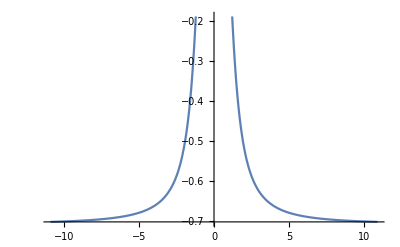

```mathematica
Plot[-(-1+x^2)/(√2 √(1+x^4)),{x,-10.92,10.92}]
```

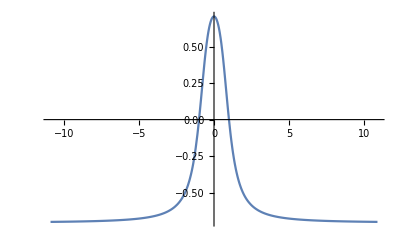

```mathematica
Plot[-(-1+x^2)/(√2 √(1+x^4)),{x,-10.92,10.92},PlotRange->Full]
```

```mathematica
FullSimplify[Normalize@{x,x^3}.Normalize@{x,x},x∈Reals]
```

(1+x^2)/(√2 √(1+x^4))

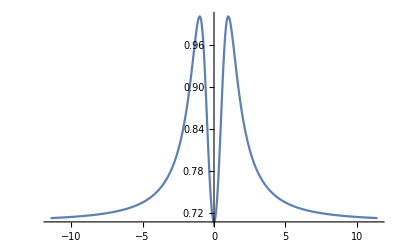

```mathematica
Plot[(1+x^2)/(√2 √(1+x^4)),{x,-11.440000000000001,11.440000000000001}]
```

```mathematica
FullSimplify[Normalize@{x,x^3}.Normalize@{x,α x},x∈Reals]
```

(x^2+x^4 α)/(√((x^4+x^8) (1+Abs[α]^2)))

```mathematica
FullSimplify[Normalize@{x,x^3}.Normalize@{x,α x},{x,α}∈Reals]
```

(1+x^2 α)/(√((1+x^4) (1+α^2)))

```mathematica
Manipulate[Plot[(1+x^2 α)/(√((1+x^4) (1+α^2))),{x,-1.0602878999079475,1.0602878999079475}],{α,-1.2863733215943343,1.2863733215943343}]
```

```mathematica
Plot3D[(1+x^2 α)/(√((1+x^4) (1+α^2))),{x,-3,3},{α,-10,10}]
```

-Graphics3D-

```mathematica
D[(1+x^2 α)/(√((1+x^4) (1+α^2))),α]==0
```

-((1+x^4) α (1+x^2 α))/(((1+x^4) (1+α^2))^(3/2))+x^2/(√((1+x^4) (1+α^2)))==0

```mathematica
FullSimplify[-((1+x^4) α (1+x^2 α))/(((1+x^4) (1+α^2))^(3/2))+x^2/(√((1+x^4) (1+α^2)))==0,{x,α}∈Reals]
```

x^2==α

```mathematica
FullSimplify[Normalize@{x,x^3}.Normalize@{x,α x},{x,α}∈Reals]==0
```

(1+x^2 α)/(√((1+x^4) (1+α^2)))==0

```mathematica
Reduce[(1+x^2 α)/(√((1+x^4) (1+α^2)))==0]
```

(α≠0&&√(((1+α^2)^2)/α^2)≠0&&x==-ⅈ/(√α))||(α≠0&&√(((1+α^2)^2)/α^2)≠0&&x==ⅈ/(√α))

```mathematica
FullSimplify[Normalize@{x,x^3}.Normalize@{x,α x}==0,{x,α}∈Reals]
```

(x+x^3 α)/(√((x^4+x^8) (1+α^2)))==0

```mathematica
Reduce[(x+x^3 α)/(√((x^4+x^8) (1+α^2)))==0]
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==(-1-α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(-1-α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(1+α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(1+α^2-α^2 √(Power[«2»] Power[«2»]))/α^2}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

(α≠0&&0==(-1-α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==-ⅈ/(√α))||(α≠0&&0==(-1-α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==ⅈ/(√α))||(α≠0&&0==(1+α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==-ⅈ/(√α))||(α≠0&&0==(1+α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==ⅈ/(√α))

```mathematica
FullSimplify[Normalize@{x,x^3}.Normalize@{x,α x}==0,{x,α}∈Reals∧a≠0]
```

(x+x^3 α)/(√((x^4+x^8) (1+α^2)))==0

```mathematica
Reduce[FullSimplify[Normalize@{x,x^3}.Normalize@{x,α x}==0,{x,α}∈Reals∧a≠0]]
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==(-1-α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(-1-α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(1+α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(1+α^2-α^2 √(Power[«2»] Power[«2»]))/α^2}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

(α≠0&&0==(-1-α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==-ⅈ/(√α))||(α≠0&&0==(-1-α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==ⅈ/(√α))||(α≠0&&0==(1+α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==-ⅈ/(√α))||(α≠0&&0==(1+α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==ⅈ/(√α))

```mathematica
FullSimplify[Reduce[FullSimplify[Normalize@{x,x^3}.Normalize@{x,α x}==0,{x,α}∈Reals]],a≠0]
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==(-1-α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(-1-α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(1+α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(1+α^2-α^2 √(Power[«2»] Power[«2»]))/α^2}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

(1+1/α^2+√(((1+α^2)^2)/α^4)==0||√(((1+α^2)^2)/α^4)==1+1/α^2)&&(x==-ⅈ/(√α)||x==ⅈ/(√α))&&α≠0&&√(((1+α^2)^2)/α^4)≠0

```mathematica
Manipulate[
With[{f=Function[x,x^3+α x]},
Plot[FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals],{x,-3,3},PlotRange->{-5,5}]
],{α,-10,10}]
```

```mathematica
Manipulate[
With[{f=Function[x,x^3+α x]},
Plot[FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals],{x,-3,3},PlotRange->{-10,10}]
],{α,-10,10}]
```

```mathematica
FullSimplify[Normalize@D[{x,x^3},x].Normalize@D[{x,x},x],x∈Reals]
```

(1+3 x^2)/(√(2+18 x^4))

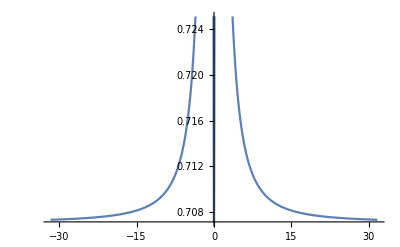

```mathematica
Plot[(1+3 x^2)/(√(2+18 x^4)),{x,-31.72,31.72}]
```

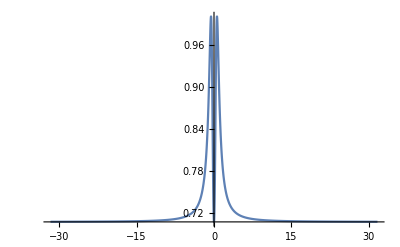

```mathematica
Plot[(1+3 x^2)/(√(2+18 x^4)),{x,-31.72,31.72},PlotRange->Full]
```

```mathematica
FullSimplify[Normalize@D[{x,x^3},x].Normalize@D[{x,a x},x],x∈Reals]
```

(1+3 a x^2)/(√((1+9 x^4) (1+Abs[a]^2)))

```mathematica
Manipulate[
With[{f=Function[x,(1+3 a x^2)/(√((1+9 x^4) (1+a^2)))]},
Plot[FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals],{x,-3,3},PlotRange->{-5,5}]
],{a,-2,2}]
```

```mathematica
Manipulate[
With[{f=Function[x,(1+3 a x^2)/(√((1+9 x^4) (1+a^2)))]},
Plot[FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals],{x,-3,3},PlotRange->{-5,5}]
],{a,-20,20}]
```

```mathematica
FullSimplify[Normalize@{x,x^3}.Normalize@{x,α x}==0,{x,α}∈Reals∧a≠0]
```

(x+x^3 α)/(√((x^4+x^8) (1+α^2)))==0

```mathematica
Reduce[(x+x^3 α)/(√((x^4+x^8) (1+α^2)))==0]
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==(-1-α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(-1-α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(1+α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(1+α^2-α^2 √(Power[«2»] Power[«2»]))/α^2}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

(α≠0&&0==(-1-α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==-ⅈ/(√α))||(α≠0&&0==(-1-α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==ⅈ/(√α))||(α≠0&&0==(1+α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==-ⅈ/(√α))||(α≠0&&0==(1+α^2-α^2 √(((1+α^2)^2)/α^4))/α^2&&√(((1+α^2)^2)/α^4)≠0&&x==ⅈ/(√α))

```mathematica
FullSimplify[Reduce[FullSimplify[Normalize@{x,x^3}.Normalize@{x,α x}==0,{x,α}∈Reals∧a≠0],a],a∈Reals]
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==(-1-α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(-1-α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(1+α^2-α^2 √(Power[«2»] Power[«2»]))/α^2,0==(1+α^2-α^2 √(Power[«2»] Power[«2»]))/α^2}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

(1+1/α^2+√(((1+α^2)^2)/α^4)==0||√(((1+α^2)^2)/α^4)==1+1/α^2)&&(x==-ⅈ/(√α)||x==ⅈ/(√α))&&α≠0&&√(((1+α^2)^2)/α^4)≠0

```mathematica
Solve[1+1/α^2+√(((1+α^2)^2)/α^4)==0,α]
```

{{}}

```mathematica
1+1/α^2+√(((1+α^2)^2)/α^4)
```

1+1/α^2+√(((1+α^2)^2)/α^4)

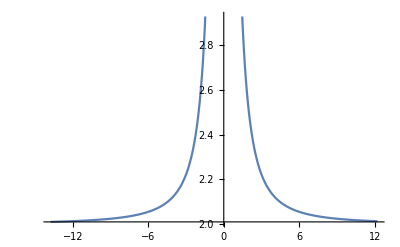

```mathematica
Plot[1+1/α^2+√(((1+α^2)^2)/α^4),{α,-13.776577576937402,12.223422423062596}]
```

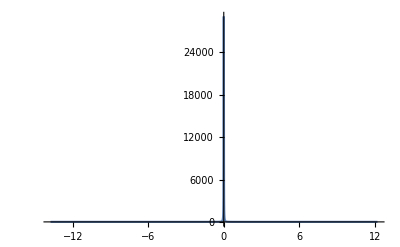

```mathematica
Plot[1+1/α^2+√(((1+α^2)^2)/α^4),{α,-13.776577576937402,12.223422423062596},PlotRange->Full]
```

```mathematica
x^3-10x
```

-10 x+x^3

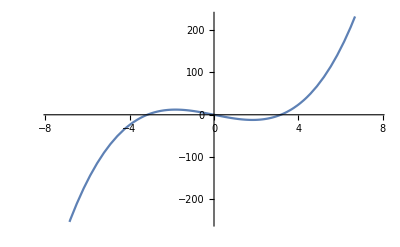

```mathematica
Plot[-10 x+x^3,{x,-7.745966692414833,7.745966692414833}]
```

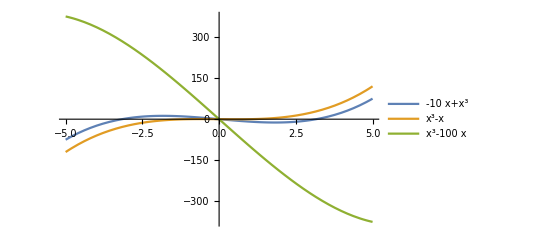

```mathematica
Plot[{-10 x+x^3,x^3-x,x^3-100x},{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
Manipulate[
With[{f=Function[x,(x^3-x)/x^a]},
Plot[FullSimplify[f''[x]/((√(1+f'[x]^2))^3),x∈Reals],{x,-3,3},PlotRange->{-5,5}]
],{a,-20,20}]
```

```mathematica
Table[(x^3-x)/x^a,{a,0,20}]
```

{-x+x^3,(-x+x^3)/x,(-x+x^3)/x^2,(-x+x^3)/x^3,(-x+x^3)/x^4,(-x+x^3)/x^5,(-x+x^3)/x^6,(-x+x^3)/x^7,(-x+x^3)/x^8,(-x+x^3)/x^9,(-x+x^3)/x^10,(-x+x^3)/x^11,(-x+x^3)/x^12,(-x+x^3)/x^13,(-x+x^3)/x^14,(-x+x^3)/x^15,(-x+x^3)/x^16,(-x+x^3)/x^17,(-x+x^3)/x^18,(-x+x^3)/x^19,(-x+x^3)/x^20}

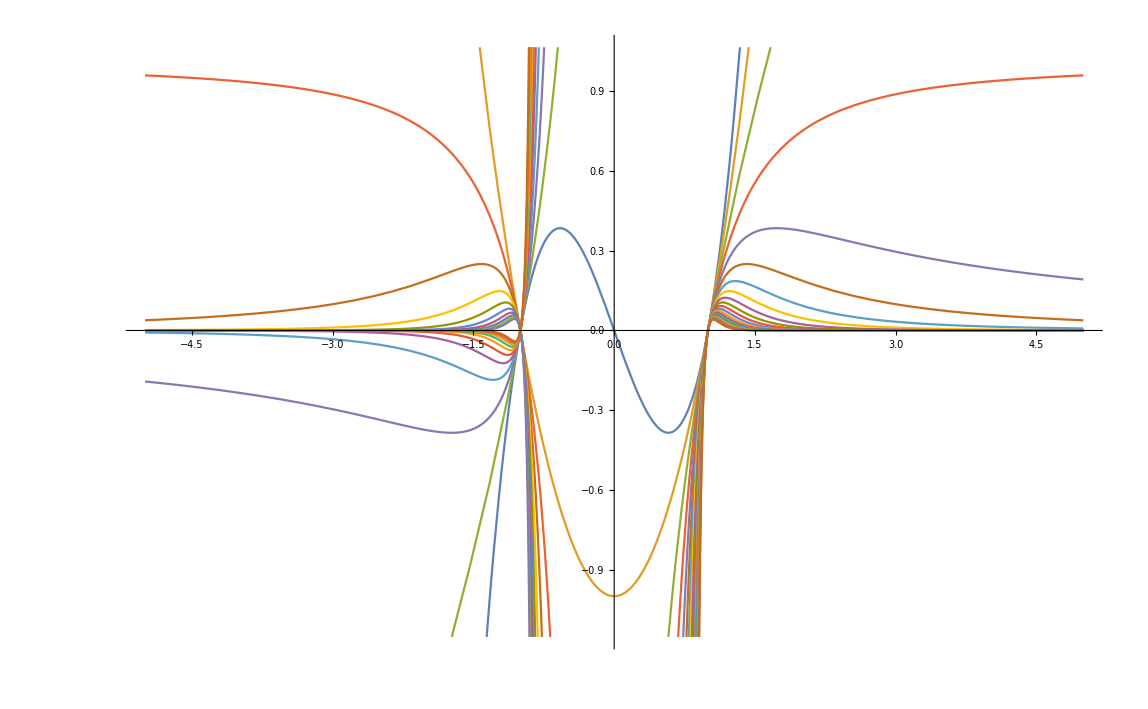

```mathematica
Plot[
{-x+x^3,(-x+x^3)/x,(-x+x^3)/x^2,(-x+x^3)/x^3,(-x+x^3)/x^4,(-x+x^3)/x^5,(-x+x^3)/x^6,(-x+x^3)/x^7,(-x+x^3)/x^8,(-x+x^3)/x^9,(-x+x^3)/x^10,(-x+x^3)/x^11,(-x+x^3)/x^12,(-x+x^3)/x^13,(-x+x^3)/x^14,(-x+x^3)/x^15,(-x+x^3)/x^16,(-x+x^3)/x^17,(-x+x^3)/x^18,(-x+x^3)/x^19,(-x+x^3)/x^20}
,{x,-5,5}]
```

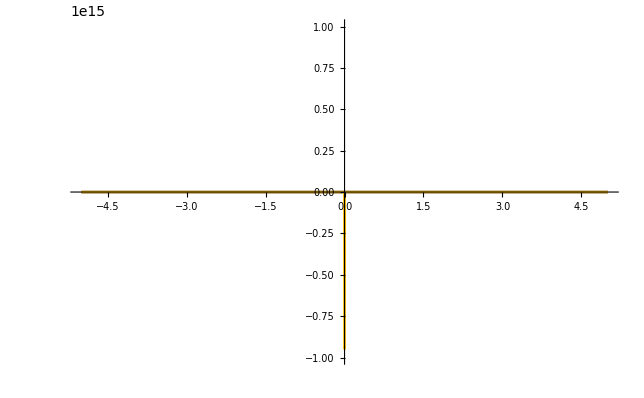

```mathematica
Plot[
{-x+x^3,(-x+x^3)/x,(-x+x^3)/x^2,(-x+x^3)/x^3,(-x+x^3)/x^4,(-x+x^3)/x^5,(-x+x^3)/x^6,(-x+x^3)/x^7,(-x+x^3)/x^8,(-x+x^3)/x^9,(-x+x^3)/x^10,(-x+x^3)/x^11,(-x+x^3)/x^12,(-x+x^3)/x^13,(-x+x^3)/x^14,(-x+x^3)/x^15,(-x+x^3)/x^16,(-x+x^3)/x^17,(-x+x^3)/x^18,(-x+x^3)/x^19,(-x+x^3)/x^20}
,{x,-5,5},PlotRange->Full]
```

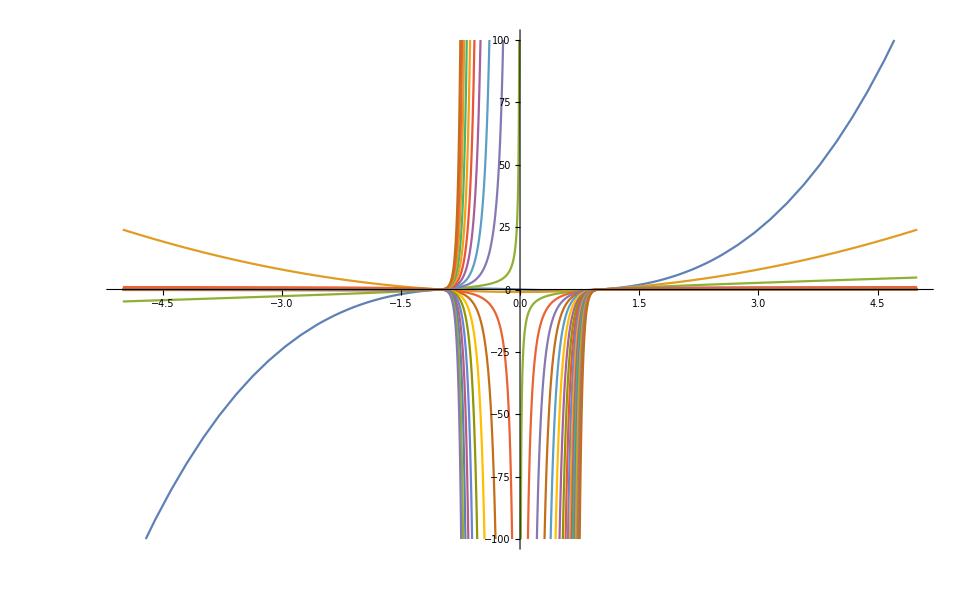

```mathematica
Plot[
{-x+x^3,(-x+x^3)/x,(-x+x^3)/x^2,(-x+x^3)/x^3,(-x+x^3)/x^4,(-x+x^3)/x^5,(-x+x^3)/x^6,(-x+x^3)/x^7,(-x+x^3)/x^8,(-x+x^3)/x^9,(-x+x^3)/x^10,(-x+x^3)/x^11,(-x+x^3)/x^12,(-x+x^3)/x^13,(-x+x^3)/x^14,(-x+x^3)/x^15,(-x+x^3)/x^16,(-x+x^3)/x^17,(-x+x^3)/x^18,(-x+x^3)/x^19,(-x+x^3)/x^20}
,{x,-5,5},PlotRange->{-100,100}]
```

```mathematica
Table[(x^3-x)/x^-a,{a,0,20}]
```

{-x+x^3,x (-x+x^3),x^2 (-x+x^3),x^3 (-x+x^3),x^4 (-x+x^3),x^5 (-x+x^3),x^6 (-x+x^3),x^7 (-x+x^3),x^8 (-x+x^3),x^9 (-x+x^3),x^10 (-x+x^3),x^11 (-x+x^3),x^12 (-x+x^3),x^13 (-x+x^3),x^14 (-x+x^3),x^15 (-x+x^3),x^16 (-x+x^3),x^17 (-x+x^3),x^18 (-x+x^3),x^19 (-x+x^3),x^20 (-x+x^3)}

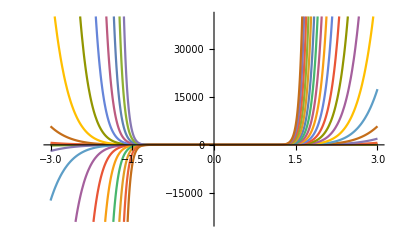

```mathematica
Plot[
{-x+x^3,x (-x+x^3),x^2 (-x+x^3),x^3 (-x+x^3),x^4 (-x+x^3),x^5 (-x+x^3),x^6 (-x+x^3),x^7 (-x+x^3),x^8 (-x+x^3),x^9 (-x+x^3),x^10 (-x+x^3),x^11 (-x+x^3),x^12 (-x+x^3),x^13 (-x+x^3),x^14 (-x+x^3),x^15 (-x+x^3),x^16 (-x+x^3),x^17 (-x+x^3),x^18 (-x+x^3),x^19 (-x+x^3),x^20 (-x+x^3)}
,{x,-3,3}]
```

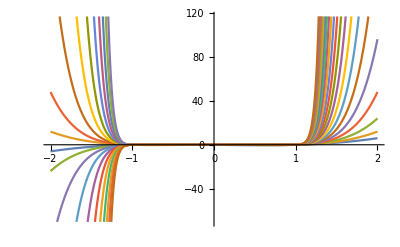

```mathematica
Plot[
{-x+x^3,x (-x+x^3),x^2 (-x+x^3),x^3 (-x+x^3),x^4 (-x+x^3),x^5 (-x+x^3),x^6 (-x+x^3),x^7 (-x+x^3),x^8 (-x+x^3),x^9 (-x+x^3),x^10 (-x+x^3),x^11 (-x+x^3),x^12 (-x+x^3),x^13 (-x+x^3),x^14 (-x+x^3),x^15 (-x+x^3),x^16 (-x+x^3),x^17 (-x+x^3),x^18 (-x+x^3),x^19 (-x+x^3),x^20 (-x+x^3)}
,{x,-2,2}]
```

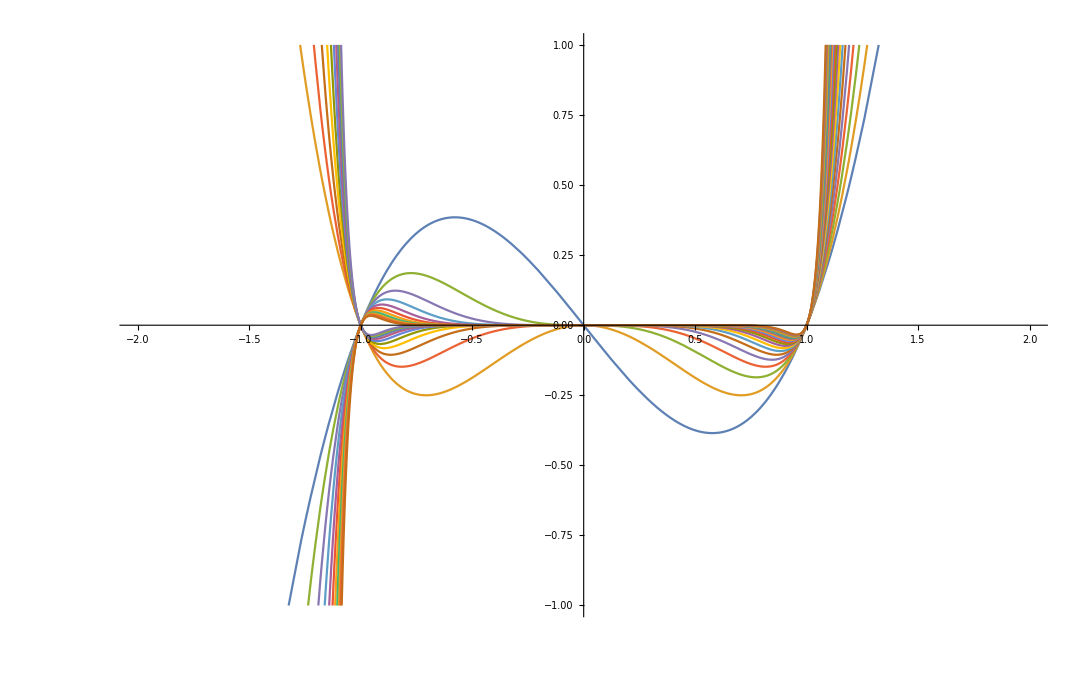

```mathematica
Plot[
{-x+x^3,x (-x+x^3),x^2 (-x+x^3),x^3 (-x+x^3),x^4 (-x+x^3),x^5 (-x+x^3),x^6 (-x+x^3),x^7 (-x+x^3),x^8 (-x+x^3),x^9 (-x+x^3),x^10 (-x+x^3),x^11 (-x+x^3),x^12 (-x+x^3),x^13 (-x+x^3),x^14 (-x+x^3),x^15 (-x+x^3),x^16 (-x+x^3),x^17 (-x+x^3),x^18 (-x+x^3),x^19 (-x+x^3),x^20 (-x+x^3)}
,{x,-2,2},PlotRange->{-1,1}]
```

```mathematica
(x^3-x)/x^-a
```

x^a (-x+x^3)

```mathematica
Manipulate[Plot[x^a (-x+x^3),{x,-2.154434690031884,2.154434690031884}],{a,-10.,10.}]
```

```mathematica
Plot3D[x^a (-x+x^3),{x,-2,2},{a,-10.,10.}]
```

-Graphics3D-

```mathematica
(x^3-x)/x^a
```

x^-a (-x+x^3)

```mathematica
With[{f=Function[x,(x^3-x)/x^a]},
FullSimplify[f''[x]/((√(1+f'[x]^2))^3),Element[x,Reals]]
]
```

(x^(-1+a) (-(-1+a) a+(-3+a) (-2+a) x^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))

```mathematica
Manipulate[Plot[(x^(-1+a) (-(-1+a) a+(-3+a) (-2+a) x^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2)),{x,-8,8}],{a,-8,8}]
```

```mathematica
Plot3D[(x^(-1+a) (-(-1+a) a+(-3+a) (-2+a) x^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2)),{x,a}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
Plot3D[(x^(-1+a) (-(-1+a) a+(-3+a) (-2+a) x^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2)),{x,a}∈Disk[]]
```

-Graphics3D-

```mathematica
Laplacian[(x^(-1+a) (-(-1+a) a+(-3+a) (-2+a) x^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2)),{x,a}]
```

(3 x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) (4 (-3+a) x^(1-2 a) (1-a+(-3+a) x^2)-2 a x^(-1-2 a) (1-a+(-3+a) x^2)^2)^2)/(4 (x^(2 a)+(1-a+(-3+a) x^2)^2) (1+x^(-2 a) (1-a+(-3+a) x^2)^2)^(5/2))-(x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) (8 (-3+a)^2 x^(2-2 a)+4 (1-2 a) (-3+a) x^(-2 a) (1-a+(-3+a) x^2)-8 (-3+a) a x^(-2 a) (1-a+(-3+a) x^2)-2 (-1-2 a) a x^(-2-2 a) (1-a+(-3+a) x^2)^2))/(2 (x^(2 a)+(1-a+(-3+a) x^2)^2) (1+x^(-2 a) (1-a+(-3+a) x^2)^2)^(3/2))+(x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) (2 a x^(-1+2 a)+4 (-3+a) x (1-a+(-3+a) x^2)) (4 (-3+a) x^(1-2 a) (1-a+(-3+a) x^2)-2 a x^(-1-2 a) (1-a+(-3+a) x^2)^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^2 (1+x^(-2 a) (1-a+(-3+a) x^2)^2)^(3/2))-(2 (-3+a) (-2+a) x^a (4 (-3+a) x^(1-2 a) (1-a+(-3+a) x^2)-2 a x^(-1-2 a) (1-a+(-3+a) x^2)^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2) (1+x^(-2 a) (1-a+(-3+a) x^2)^2)^(3/2))-((-1+a) x^(-2+a) ((1-a) a+(-3+a) (-2+a) x^2) (4 (-3+a) x^(1-2 a) (1-a+(-3+a) x^2)-2 a x^(-1-2 a) (1-a+(-3+a) x^2)^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2) (1+x^(-2 a) (1-a+(-3+a) x^2)^2)^(3/2))+(2 x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) (2 a x^(-1+2 a)+4 (-3+a) x (1-a+(-3+a) x^2))^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3 √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))-(x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) (8 (-3+a)^2 x^2+2 a (-1+2 a) x^(-2+2 a)+4 (-3+a) (1-a+(-3+a) x^2)))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^2 √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))-(4 (-3+a) (-2+a) x^a (2 a x^(-1+2 a)+4 (-3+a) x (1-a+(-3+a) x^2)))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^2 √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))-(2 (-1+a) x^(-2+a) ((1-a) a+(-3+a) (-2+a) x^2) (2 a x^(-1+2 a)+4 (-3+a) x (1-a+(-3+a) x^2)))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^2 √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))+(2 (-3+a) (-2+a) (-1+a) x^(-1+a))/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))+(2 (-3+a) (-2+a) a x^(-1+a))/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))+(x^(-1+a) (-2+2 x^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))+((-2+a) (-1+a) x^(-3+a) ((1-a) a+(-3+a) (-2+a) x^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))+(2 x^(-1+a) (1-2 a+(-3+a) x^2+(-2+a) x^2) Log[x])/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))+(x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) Log[x]^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))-(2 x^(-1+a) (1-2 a+(-3+a) x^2+(-2+a) x^2) (2 (-1+x^2) (1-a+(-3+a) x^2)+2 x^(2 a) Log[x]))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^2 √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))-(2 x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) Log[x] (2 (-1+x^2) (1-a+(-3+a) x^2)+2 x^(2 a) Log[x]))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^2 √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))+(2 x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) (2 (-1+x^2) (1-a+(-3+a) x^2)+2 x^(2 a) Log[x])^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3 √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))-(x^(-1+a) (1-2 a+(-3+a) x^2+(-2+a) x^2) (2 x^(-2 a) (-1+x^2) (1-a+(-3+a) x^2)-2 x^(-2 a) (1-a+(-3+a) x^2)^2 Log[x]))/((x^(2 a)+(1-a+(-3+a) x^2)^2) (1+x^(-2 a) (1-a+(-3+a) x^2)^2)^(3/2))-(x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) Log[x] (2 x^(-2 a) (-1+x^2) (1-a+(-3+a) x^2)-2 x^(-2 a) (1-a+(-3+a) x^2)^2 Log[x]))/((x^(2 a)+(1-a+(-3+a) x^2)^2) (1+x^(-2 a) (1-a+(-3+a) x^2)^2)^(3/2))+(x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) (2 (-1+x^2) (1-a+(-3+a) x^2)+2 x^(2 a) Log[x]) (2 x^(-2 a) (-1+x^2) (1-a+(-3+a) x^2)-2 x^(-2 a) (1-a+(-3+a) x^2)^2 Log[x]))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^2 (1+x^(-2 a) (1-a+(-3+a) x^2)^2)^(3/2))+(3 x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) (2 x^(-2 a) (-1+x^2) (1-a+(-3+a) x^2)-2 x^(-2 a) (1-a+(-3+a) x^2)^2 Log[x])^2)/(4 (x^(2 a)+(1-a+(-3+a) x^2)^2) (1+x^(-2 a) (1-a+(-3+a) x^2)^2)^(5/2))-(x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) (2 (-1+x^2)^2+4 x^(2 a) Log[x]^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^2 √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))-(x^(-1+a) ((1-a) a+(-3+a) (-2+a) x^2) (2 x^(-2 a) (-1+x^2)^2-8 x^(-2 a) (-1+x^2) (1-a+(-3+a) x^2) Log[x]+4 x^(-2 a) (1-a+(-3+a) x^2)^2 Log[x]^2))/(2 (x^(2 a)+(1-a+(-3+a) x^2)^2) (1+x^(-2 a) (1-a+(-3+a) x^2)^2)^(3/2))

```mathematica
FullSimplify[Laplacian[(x^(-1+a) (-(-1+a) a+(-3+a) (-2+a) x^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2) √(1+x^(-2 a) (1-a+(-3+a) x^2)^2)),{x,a}],{x,a}∈Reals]
```

(x^(-3+a) (4 a^8 (-1+x^2)^5-2 a^7 (-1+x^2)^4 (-13+45 x^2)+2 a^6 (-1+x^2)^3 (36-266 x^2+442 x^4-5 x^(2 a))+a^5 (-1+x^2)^2 (110-1262 x^2+4678 x^4-4950 x^6+3 x^(2 a) (-9+49 x^2))+2 x^2 (x^(4 a) (-1+x^2)+2 (1-3 x^2)^2 (1+89 x^2+396 x^4)+x^(2 a) (1+140 x^2-753 x^4-36 x^6))+a^4 (-1+x^2) (100+x^(4 a)+x^(2 a) (-17+436 x^2-887 x^4)+2 x^2 (-763+4698 x^2-11454 x^4+8636 x^6+x^8))+a^2 (-16+298 x^2+x^(4 a) (1+11 x^2)+6 x^4 (-459+3894 x^2-11038 x^4+8875 x^6+9 x^8)-x^(2 a) (15+58 x^2-2658 x^4+4854 x^6+11 x^8))+a (-2 x^(4 a) (-1+3 x^2)+x^(2 a) (4-49 x^2-1321 x^4+4301 x^6+57 x^8)-2 (-1+3 x^2) (1-17 x^2-242 x^4-3272 x^6+6993 x^8+9 x^10))+a^3 (54-2 x^(4 a) (1+3 x^2)+x^(2 a) (11+387 x^2-2643 x^4+2805 x^6)-2 x^2 (490-4317 x^2+19104 x^4-33737 x^6+19214 x^8+9 x^10))+x^2 Log[x] (2 (-2 (1-a+(-3+a) x^2)^3 (-1+a^2-2 (5+(-2+a) a) x^2+(-3+a) (-1+a) x^4)+x^(4 a) (-1+5 x^2-2 a (-1+x^2))+x^(2 a) (1-a+(-3+a) x^2) (1-62 x^2+69 x^4+11 a^2 (-1+x^2)^2-4 a (3-17 x^2+14 x^4)))+(-(-1+a) a+(-3+a) (-2+a) x^2) (x^(4 a)-10 x^(2 a) (1-a+(-3+a) x^2)^2+4 (1-a+(-3+a) x^2)^4) Log[x])))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3 √(1+x^(-2 a) (1-a+(-3+a) x^2)^2))

```mathematica
Manipulate[Plot[%106,{x,-8,8}],{a,-8,8}]
```

```mathematica
Plot3D[%106,{x,-8,8},{a,-8,8}]
```

-Graphics3D-

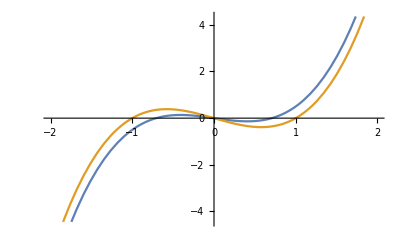

```mathematica
Plot[{x^3-x/2,x^3-x},{x,-2,2}]
```

```mathematica
With[{f=Function[x,x^3+a x]},
FullSimplify[f''[x]/((√(1+f'[x]^2))^3),Element[x|a,Reals]]
]
```

(6 x)/((1+(a+3 x^2)^2)^(3/2))

```mathematica
Manipulate[Plot[(6 x)/((1+(a+3 x^2)^2)^(3/2)),{x,-40.24704919506678,37.85501156496565}],{a,-308.6626348932162,-215.9826494859098}]
```

```mathematica
D[(6 x)/((1+(a+3 x^2)^2)^(3/2)),a]==0
```

-(18 x (a+3 x^2))/((1+(a+3 x^2)^2)^(5/2))==0

```mathematica
Reduce[-(18 x (a+3 x^2))/((1+(a+3 x^2)^2)^(5/2))==0]
```

(√(1+a^2)≠0&&x==0)||a==-3 x^2

```mathematica
(6 x)/((1+(a+3 x^2)^2)^(3/2))/.a->-3 x^2
```

6 x

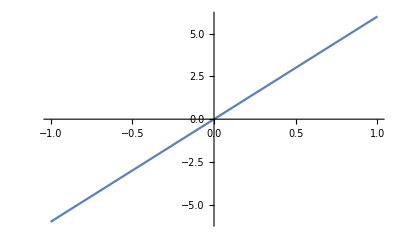

```mathematica
Plot[6 x,{x,-1,1}]
```

```mathematica
Grad[(6 x)/((1+(a+3 x^2)^2)^(3/2)),{x,a}]==0
```

{-(108 x^2 (a+3 x^2))/((1+(a+3 x^2)^2)^(5/2))+6/((1+(a+3 x^2)^2)^(3/2)),-(18 x (a+3 x^2))/((1+(a+3 x^2)^2)^(5/2))}==0

```mathematica
{-(108 x^2 (a+3 x^2))/((1+(a+3 x^2)^2)^(5/2))+6/((1+(a+3 x^2)^2)^(3/2)),-(18 x (a+3 x^2))/((1+(a+3 x^2)^2)^(5/2))}=={0,0}
```

{-(108 x^2 (a+3 x^2))/((1+(a+3 x^2)^2)^(5/2))+6/((1+(a+3 x^2)^2)^(3/2)),-(18 x (a+3 x^2))/((1+(a+3 x^2)^2)^(5/2))}=={0,0}

```mathematica
Reduce[{-(108 x^2 (a+3 x^2))/((1+(a+3 x^2)^2)^(5/2))+6/((1+(a+3 x^2)^2)^(3/2)),-(18 x (a+3 x^2))/((1+(a+3 x^2)^2)^(5/2))}=={0,0}]
```

False

```mathematica
x^3+(3 x^2)x
```

4 x^3

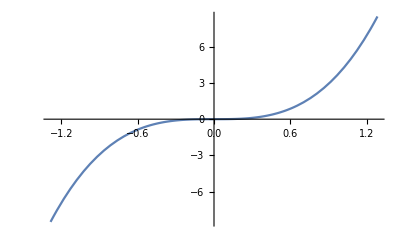

```mathematica
Plot[4 x^3,{x,-1.2851194708927707,1.2851194708927707}]
```

```mathematica
D[x^3,x]/.x->0
```

0

```mathematica
D[{x,x^3},x]/.x->0
```

{1,0}

```mathematica
-1/{1,0}
```

Power::infy: Infinite expression 1/0 encountered.

{-1,ComplexInfinity}

```mathematica
-1/D[x^3,x]
```

-1/(3 x^2)

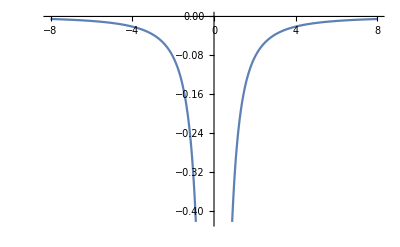

```mathematica
Plot[-1/(3 x^2),{x,-8,8}]
```

```mathematica
x^3-1/(3 x^2)
```

-1/(3 x^2)+x^3

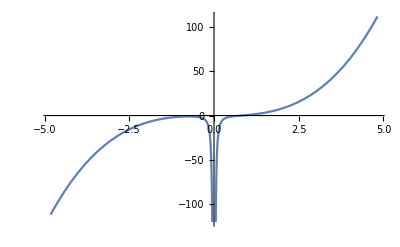

```mathematica
Plot[-1/(3 x^2)+x^3,{x,-4.824182098741111,4.824182098741111}]
```

```mathematica
With[{f=Function[x,x^3-1/(3 x^2)]},
FullSimplify[f''[x]/((√(1+f'[x]^2))^3),Element[x,Reals]]
]
```

(-2/x^4+6 x)/((1+(2/(3 x^3)+3 x^2)^2)^(3/2))

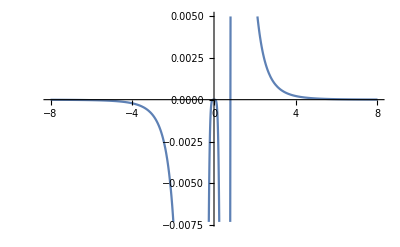

```mathematica
Plot[(-2/x^4+6 x)/((1+(2/(3 x^3)+3 x^2)^2)^(3/2)),{x,-8,8}]
```

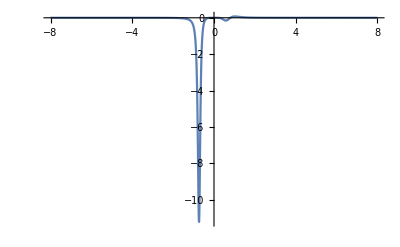

```mathematica
Plot[(-2/x^4+6 x)/((1+(2/(3 x^3)+3 x^2)^2)^(3/2)),{x,-8,8},PlotRange->Full]
```

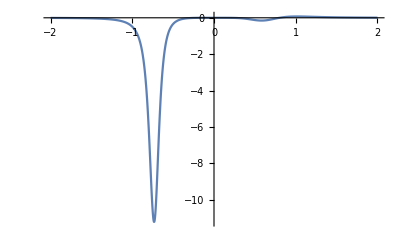

```mathematica
Plot[(-2/x^4+6 x)/((1+(2/(3 x^3)+3 x^2)^2)^(3/2)),{x,-2,2},PlotRange->Full]
```

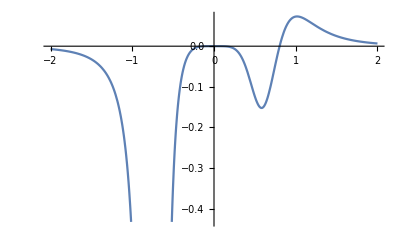

```mathematica
Plot[(-2/x^4+6 x)/((1+(2/(3 x^3)+3 x^2)^2)^(3/2)),{x,-2,2}]
```

```mathematica
FullSimplify[(-2/x^4+6 x)/((1+(2/(3 x^3)+3 x^2)^2)^(3/2))==f''[x]/((√(1+f'[x]^2))^3),{x,f[x]}∈Reals]
```

(-2/x^4+6 x)/((1+(2/(3 x^3)+3 x^2)^2)^(3/2))==f''[x]/((1+f'[x]^2)^(3/2))

```mathematica
DSolve[(-2/x^4+6 x)/((1+(2/(3 x^3)+3 x^2)^2)^(3/2))==f''[x]/((1+f'[x]^2)^(3/2)),{f[x],f[x]},{x}]
```

{{f[x]→C[2]+-(√(48 C[1]^2-16 C[1]^4+864 C[1]^2 K[1]^5-288 C[1]^4 K[1]^5+36 K[1]^6+144 C[1]^2 K[1]^6-72 C[1]^4 K[1]^6+5832 C[1]^2 K[1]^10-1944 C[1]^4 K[1]^10+324 K[1]^11+1296 C[1]^2 K[1]^11-648 C[1]^4 K[1]^11+81 C[1]^2 K[1]^12-81 C[1]^4 K[1]^12+17496 C[1]^2 K[1]^15-5832 C[1]^4 K[1]^15+729 K[1]^16+2916 C[1]^2 K[1]^16-1458 C[1]^4 K[1]^16+19683 C[1]^2 K[1]^20-6561 C[1]^4 K[1]^20+16 C[1] √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)+216 C[1] K[1]^5 √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)+36 C[1] K[1]^6 √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)+972 C[1] K[1]^10 √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)+162 C[1] K[1]^11 √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)+1458 C[1] K[1]^15 √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)))/(√(-64 C[1]^2+16 C[1]^4-1152 C[1]^2 K[1]^5+288 C[1]^4 K[1]^5-216 C[1]^2 K[1]^6+72 C[1]^4 K[1]^6-7776 C[1]^2 K[1]^10+1944 C[1]^4 K[1]^10-1944 C[1]^2 K[1]^11+648 C[1]^4 K[1]^11+81 K[1]^12-162 C[1]^2 K[1]^12+81 C[1]^4 K[1]^12-23328 C[1]^2 K[1]^15+5832 C[1]^4 K[1]^15-4374 C[1]^2 K[1]^16+1458 C[1]^4 K[1]^16-26244 C[1]^2 K[1]^20+6561 C[1]^4 K[1]^20))K[1]1x},{f[x]→C[2]+(√(48 C[1]^2-16 C[1]^4+864 C[1]^2 K[2]^5-288 C[1]^4 K[2]^5+36 K[2]^6+144 C[1]^2 K[2]^6-72 C[1]^4 K[2]^6+5832 C[1]^2 K[2]^10-1944 C[1]^4 K[2]^10+324 K[2]^11+1296 C[1]^2 K[2]^11-648 C[1]^4 K[2]^11+81 C[1]^2 K[2]^12-81 C[1]^4 K[2]^12+17496 C[1]^2 K[2]^15-5832 C[1]^4 K[2]^15+729 K[2]^16+2916 C[1]^2 K[2]^16-1458 C[1]^4 K[2]^16+19683 C[1]^2 K[2]^20-6561 C[1]^4 K[2]^20+16 C[1] √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)+216 C[1] K[2]^5 √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)+36 C[1] K[2]^6 √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)+972 C[1] K[2]^10 √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)+162 C[1] K[2]^11 √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)+1458 C[1] K[2]^15 √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)))/(√(-64 C[1]^2+16 C[1]^4-1152 C[1]^2 K[2]^5+288 C[1]^4 K[2]^5-216 C[1]^2 K[2]^6+72 C[1]^4 K[2]^6-7776 C[1]^2 K[2]^10+1944 C[1]^4 K[2]^10-1944 C[1]^2 K[2]^11+648 C[1]^4 K[2]^11+81 K[2]^12-162 C[1]^2 K[2]^12+81 C[1]^4 K[2]^12-23328 C[1]^2 K[2]^15+5832 C[1]^4 K[2]^15-4374 C[1]^2 K[2]^16+1458 C[1]^4 K[2]^16-26244 C[1]^2 K[2]^20+6561 C[1]^4 K[2]^20))K[2]1x}}

```mathematica
FullSimplify[(-2/x^4+6 x)/((1+(2/(3 x^3)+3 x^2)^2)^(3/2))==f''[x]/((√(1+f'[x]^2))^3),x∈Reals]
```

(-2/x^4+6 x)/((1+(2/(3 x^3)+3 x^2)^2)^(3/2))==f''[x]/((1+f'[x]^2)^(3/2))

```mathematica
DSolve[(-2/x^4+6 x)/((1+(2/(3 x^3)+3 x^2)^2)^(3/2))==f''[x]/((1+f'[x]^2)^(3/2)),{f[x],f[x]},{x}]
```

{{f[x]→C[2]+-(√(48 C[1]^2-16 C[1]^4+864 C[1]^2 K[1]^5-288 C[1]^4 K[1]^5+36 K[1]^6+144 C[1]^2 K[1]^6-72 C[1]^4 K[1]^6+5832 C[1]^2 K[1]^10-1944 C[1]^4 K[1]^10+324 K[1]^11+1296 C[1]^2 K[1]^11-648 C[1]^4 K[1]^11+81 C[1]^2 K[1]^12-81 C[1]^4 K[1]^12+17496 C[1]^2 K[1]^15-5832 C[1]^4 K[1]^15+729 K[1]^16+2916 C[1]^2 K[1]^16-1458 C[1]^4 K[1]^16+19683 C[1]^2 K[1]^20-6561 C[1]^4 K[1]^20+16 C[1] √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)+216 C[1] K[1]^5 √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)+36 C[1] K[1]^6 √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)+972 C[1] K[1]^10 √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)+162 C[1] K[1]^11 √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)+1458 C[1] K[1]^15 √(4+36 K[1]^5+9 K[1]^6+81 K[1]^10)))/(√(-64 C[1]^2+16 C[1]^4-1152 C[1]^2 K[1]^5+288 C[1]^4 K[1]^5-216 C[1]^2 K[1]^6+72 C[1]^4 K[1]^6-7776 C[1]^2 K[1]^10+1944 C[1]^4 K[1]^10-1944 C[1]^2 K[1]^11+648 C[1]^4 K[1]^11+81 K[1]^12-162 C[1]^2 K[1]^12+81 C[1]^4 K[1]^12-23328 C[1]^2 K[1]^15+5832 C[1]^4 K[1]^15-4374 C[1]^2 K[1]^16+1458 C[1]^4 K[1]^16-26244 C[1]^2 K[1]^20+6561 C[1]^4 K[1]^20))K[1]1x},{f[x]→C[2]+(√(48 C[1]^2-16 C[1]^4+864 C[1]^2 K[2]^5-288 C[1]^4 K[2]^5+36 K[2]^6+144 C[1]^2 K[2]^6-72 C[1]^4 K[2]^6+5832 C[1]^2 K[2]^10-1944 C[1]^4 K[2]^10+324 K[2]^11+1296 C[1]^2 K[2]^11-648 C[1]^4 K[2]^11+81 C[1]^2 K[2]^12-81 C[1]^4 K[2]^12+17496 C[1]^2 K[2]^15-5832 C[1]^4 K[2]^15+729 K[2]^16+2916 C[1]^2 K[2]^16-1458 C[1]^4 K[2]^16+19683 C[1]^2 K[2]^20-6561 C[1]^4 K[2]^20+16 C[1] √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)+216 C[1] K[2]^5 √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)+36 C[1] K[2]^6 √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)+972 C[1] K[2]^10 √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)+162 C[1] K[2]^11 √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)+1458 C[1] K[2]^15 √(4+36 K[2]^5+9 K[2]^6+81 K[2]^10)))/(√(-64 C[1]^2+16 C[1]^4-1152 C[1]^2 K[2]^5+288 C[1]^4 K[2]^5-216 C[1]^2 K[2]^6+72 C[1]^4 K[2]^6-7776 C[1]^2 K[2]^10+1944 C[1]^4 K[2]^10-1944 C[1]^2 K[2]^11+648 C[1]^4 K[2]^11+81 K[2]^12-162 C[1]^2 K[2]^12+81 C[1]^4 K[2]^12-23328 C[1]^2 K[2]^15+5832 C[1]^4 K[2]^15-4374 C[1]^2 K[2]^16+1458 C[1]^4 K[2]^16-26244 C[1]^2 K[2]^20+6561 C[1]^4 K[2]^20))K[2]1x}}

```mathematica
FullSimplify[==f''[x]/((√(1+f'[x]^2))^3),{x,f[x]}∈Reals]
```

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
FullSimplify[ⅇ^(-x^2/2)==f''[x]/((√(1+f'[x]^2))^3),{x,f[x]}∈Reals]
```

(ⅇ^(x^2/2) f''[x])/((1+f'[x]^2)^(3/2))==1

```mathematica
DSolve[(ⅇ^(x^2/2) f''[x])/((1+f'[x]^2)^(3/2))==1,{f[x],f[x]},{x}]
```

{{f[x]→C[2]+-(√(-2 C[1]^2-2 √(2 π) C[1] Erf[K[1]/(√2)]-π Erf[K[1]/(√2)]^2))/(√(-2+2 C[1]^2+2 √(2 π) C[1] Erf[K[1]/(√2)]+π Erf[K[1]/(√2)]^2))K[1]1x},{f[x]→C[2]+(√(-2 C[1]^2-2 √(2 π) C[1] Erf[K[2]/(√2)]-π Erf[K[2]/(√2)]^2))/(√(-2+2 C[1]^2+2 √(2 π) C[1] Erf[K[2]/(√2)]+π Erf[K[2]/(√2)]^2))K[2]1x}}